```mathematica
HPL={{-426.75,0.52},{-419.98,0.6},{-412.593,0.71},{-405.91,0.8},{-399.79,0.9},{-394.12,1.},{-388.83,1.1},{-370.37,1.5},{-351.26,2.},{-320.033,3.},{-293.51,4.},{-268.91,5.},{-243.93,6.},{-241.29,6.15},{-238.59,6.2},{-235.82,6.3},{-232.99,6.4},{-230.06,6.5},{-227.02,6.65},{-222.84,6.73},{-218.33,6.86},{-213.31,6.99},{-212.9,7.},{-208.43,7.15},{-203.07,7.2},{-195.66,7.3},{-189.452,7.35005},{-174.53,7.38}};
HPV={{-177.65,7.38},{-157.51,7.355},{-149.6,7.3},{-140.66,7.2},{-134.62,7.105},{-129.87,7.},{-125.881,6.9},{-122.41,6.8},{-119.31,6.7},{-116.51,6.605},{-113.94,6.5},{-111.56,6.4},{-109.34,6.3},{-107.26,6.2},{-105.31,6.105},{-103.461,6.},{-100.05,5.8},{-98.461,5.7},{-96.95,5.605},{-95.5,5.5},{-89.12,5.},{-87.99,4.9},{-86.9,4.8},{-85.86,4.7},{-84.851,4.605},{-83.88,4.5},{-79.53,4.},{-75.98,3.5},{-73.17,3.},{-72.04,2.75},{-71.12,2.5},{-70.4,2.25},{-69.93,2.},{-69.74,1.8},{-69.72,1.7},{-69.76,1.6},{-69.851,1.5},{-70.24,1.3},{-70.56,1.2},{-70.97,1.1},{-71.48,1.},{-72.13,0.9},{-72.92,0.8},{-73.91,0.701},{-75.13,0.6},{-76.36,0.52}};
Quiet@Solve[0.52+Length[HPV]*d==7.38,d]
```

{{d→0.14913}}

```mathematica
Manipulate[
Module[{R,Tref,Pref,Tc,Pc,CpA,CpB,CpC,CpD,Hig,Hdepref,ω,κ,A,B,a2,a1,a0,q,m,r,Z,Hdep,H,p1,p2,Z1,Z2,PHiso,H1},
R=0.008314;Tref=298;Pref=0.1;
Tc=304.2;Pc=7.382;

CpA=0.0198;CpB=0.07344;CpC=-5.602*10^-8;CpD=1.715*10^-11;

Hig=CpA*(T-Tref)+1/2*CpB*(T^2-Tref^2)+1/3*CpC*(T^3-Tref^3)+1/4*CpD*(T^4-Tref^4);
Hdepref=-0.04129930622;

ω=0.228;
κ=0.37464+1.54226*ω-0.26992*ω^2;

A=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc^2*P)/(T^2*Pc);
B=0.0777960739*(P*Tc)/(Pc*T);

(*ROOTS*)
a2=B-1;
a1=A-3*B^2-2*B;
a0=-(A*B-B^2-B^3);

q=(2*a2^3-9*a2*a1+27*a0)/27;
m=(3*a1-a2^2)/3;

r=q^2/4+m^3/27;

(*g=Table[{r,P},{P,0.5,20},{T,Tc,Tc+210,20}];*)

(*Z1=Table[{T,CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]-a2/3},{P,0.5,20},{T,Tc,Tc+210,20}];
Z2=Table[Table[{T,CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]-a2/3},{P,0.5,20}],{T,Tc,Tc+210,20}];*)

Z=CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]-a2/3;

(*H1=R*T*(Z-1-A/(2.8284*B)*(1+κ*√(T/(Tc*(1+κ*(1-√(T/Tc)))^2)))*Log[(Z+2.4142*B)/(Z-0.4142*B)])-Hdepref+Hig;*)
Hdep=R*T*(Z-1-A/(2.8284*B)*(1+κ*√(T/(Tc*(1+κ*(1-√(T/Tc)))^2)))*Log[(Z+2.4142*B)/(Z-0.4142*B)]);
(*PHiso=Table[Table[{Hdep,P},{P,0.5,20}],{T,Tc,Tc+210,20}];*)
(*PHiso=Table[{Table[Hdep,{T,Tc,Tc+210,20}],P},{P,0.5,20}];*)
(*PHiso=Table[{Hdep,P},{P,0.5,20},{T,Tc,Tc+210,20}];*)
(*H=Table[Table[{Hdep-Hdepref+Hig,P},{P,0.5,20}],{T,Tc,Tc+210,20}];*)
H=Table[{-(Hdep-Hdepref+Hig),P},{P,0.5,20}];

p1=Show[
ListLogPlot[{HPL,HPV},Joined->True,PlotStyle->{{Thick,Black}},PlotRange->{0.52,20}],
Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},ImageSize->550,PlotLabel->"carbon dioxide"];
p2=ListLogPlot[H,Joined->True,PlotRange->{0.52,20}];

Switch[cs,1,Show[p1],2,Show[p1,p2],3,Show[p2]]
],
Control[{{cs,1,""},{1->" p1 ",2->" p1+p2 ",3->" p2 "},Setter}],
Control[{{T,315,"temperature (K)"},(*304.2,514.2,0.1,*)300,317,1,Appearance->"Labeled"}],SaveDefinitions->True]
```

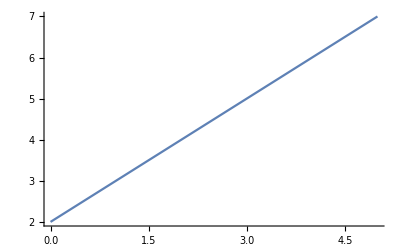

```mathematica
Module[{f},
f[x_,y_]=x+y;
Plot[f[x,2],{x,0,5}]
]
```

```mathematica
304.2+210
```

514.2

```mathematica
{300,317}-273
```

{27,44}